```mathematica
Maximos = List[{549, 0.4089076}, {581, 0.6898333}, {623, 0.8582908}, {674, 0.9074837}, {739, 0.9136308}, {822, 0.9143469}, {931, 9.148735}, {1081, 0.915417}]
```

{{549,0.408908},{581,0.689833},{623,0.858291},{674,0.907484},{739,0.913631},{822,0.914347},{931,9.14874},{1081,0.915417}}

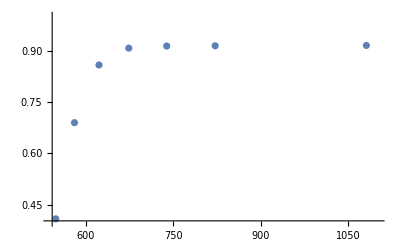

```mathematica
p2 = ListPlot[Maximos, PlotRange -> {{540, 1100}, {0.4, 1.0}}]
```

```mathematica
Maximos1 = List[{549, 0.4089076}, {581, 0.6898333}, {623, 0.8582908}, {674, 0.9074837}, {739, 0.9136308}]
```

{{549,0.408908},{581,0.689833},{623,0.858291},{674,0.907484},{739,0.913631}}

```mathematica
Maximos2 = List[{822, 0.9143469}, {931, 9.148735}, {1081, 0.915417}]
```

{{822,0.914347},{931,9.14874},{1081,0.915417}}

```mathematica
Polin1 = Fit[Maximos1, {1, x, x^2, x^3, x^4, x^5, x^6, x^7, x^8},x]
```

-35.8213+0.0811269 x+0.0000575861 x^2-8.24222×10^-8 x^3-1.99735×10^-10 x^4-1.01387×10^-13 x^5+2.77914×10^-16 x^6+5.5642×10^-19 x^7-5.81518×10^-22 x^8

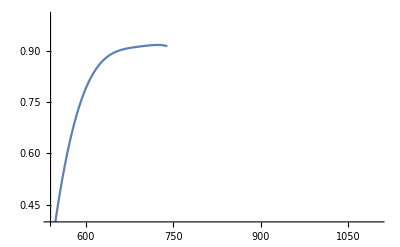

```mathematica
q1 =Plot[Polin1, {x, 540, 740}, PlotRange -> {{540, 1100},{0.4, 1.0}}]
```

```mathematica
Polin2 =  (4.10085*(10^-6)*x)+0.911005
```

0.911005+4.10085×10^-6 x

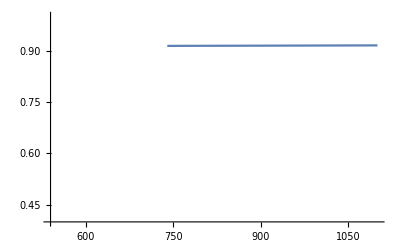

```mathematica
q2 = Plot[Polin2, {x, 740, 1100}, PlotRange -> {{540, 1100},{0.4, 1.0}}]
```

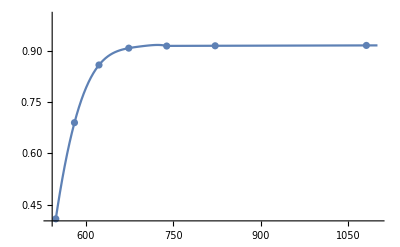

```mathematica
Show[p2, q1, q2]
```

```mathematica
Minimos = List[{561, 0.3518873}, {599, 0.4558737}, {646, 0.4991873}, {704, 0.5144687}, {778, 0.5239854}, {872, 0.5311490}, {998, 0.5372684}]
```

{{561,0.351887},{599,0.455874},{646,0.499187},{704,0.514469},{778,0.523985},{872,0.531149},{998,0.537268}}

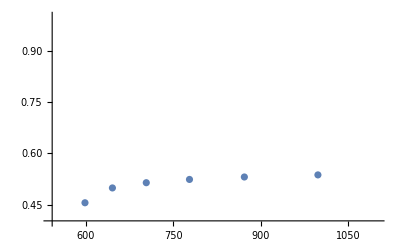

```mathematica
m1 = ListPlot[Minimos, PlotRange -> {{540, 1100}, {0.4, 1.0}}]
```

```mathematica
Pol = Fit[Minimos,{1, x, x^2, x^3, x^4},x]
```

-25.6715+0.131506 x-0.000246066 x^2+2.03217×10^-7 x^3-6.24503×10^-11 x^4

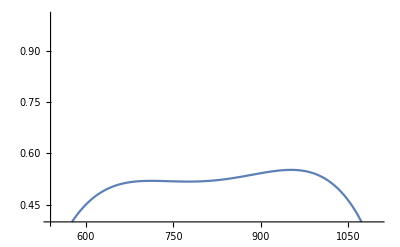

```mathematica
o1 = Plot[Pol, {x, 540, 1100}, PlotRange -> {{540, 1100},{0.4, 1.0}}]
```

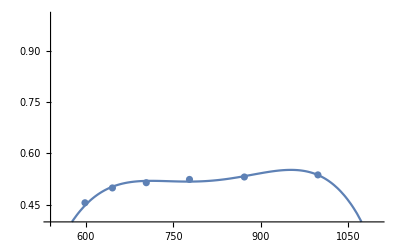

```mathematica
Show[o1, m1]
```